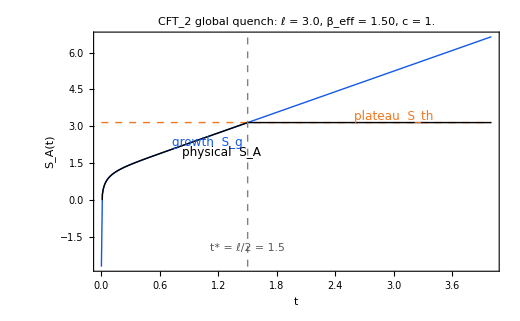

```mathematica
(* =====CFT2 global quench=====*)ClearAll[safeLogSinh,SGrowth,SThermal,SQuench,plotQuenchPrettySafe];

(*avoid log(0):floor the sinh at a tiny positive number*)
safeLogSinh[u_?NumericQ]:=Log[Max[Sinh[u],10^-300]];

(*growth branch:ℓ->2 t*)
SGrowth[c_,t_?NumericQ,betaEff_,eps_]:=(c/3) (Log[betaEff/(Pi eps)]+safeLogSinh[(2 Pi t)/betaEff]);

(*thermal plateau (time–independent)*)
SThermal[c_,ell_,betaEff_,eps_]:=(c/3) (Log[betaEff/(Pi eps)]+safeLogSinh[(Pi ell)/betaEff]);

(*physical entropy=min(growth,plateau)*)
SQuench[c_,ell_,betaEff_,eps_][t_?NumericQ]:=Min[SGrowth[c,t,betaEff,eps],SThermal[c,ell,betaEff,eps]];

plotQuenchPrettySafe[c_:1.,ell_:3.,betaEff_:1.5,eps_:0.01,tmax_:4.]:=Module[{Sg,Sp,Sq,t0,ts,dataG,dataP,dataQ,tstar,yVals,yMin,yMax,colG=RGBColor[0.08,0.35,0.90],colP=RGBColor[0.94,0.47,0.13]},Sg[t_]:=SGrowth[c,t,betaEff,eps];
Sp=SThermal[c,ell,betaEff,eps];
Sq[t_]:=Min[Sg[t],Sp];
t0=1.*10^-6*betaEff;(*start>0 to avoid t=0 exactly*)ts=N@Subdivide[t0,tmax,400];
dataG=Transpose[{ts,Sg/@ts}];
dataP=Transpose[{ts,ConstantArray[Sp,Length@ts]}];
dataQ=Transpose[{ts,Sq/@ts}];
(*finite y-range only*)yVals=Select[Last/@Join[dataG,dataP,dataQ],NumberQ[#]&&FreeQ[#,_DirectedInfinity|Indeterminate]&];
{yMin,yMax}={Min[yVals],Max[yVals]};
tstar=ell/2.;
Show[{ListLinePlot[dataG,PlotStyle->{colG,Thick}],ListLinePlot[dataP,PlotStyle->{colP,Dashed,Thick}],ListLinePlot[dataQ,PlotStyle->{Black,Thick}]},Frame->True,FrameLabel->{"t","S_A(t)"},PlotRange->{All,{yMin,yMax}},Epilog->{{GrayLevel[.5],Dashed,Line[{{tstar,yMin},{tstar,yMax}}]},Text[Style["growth  S_g",12,colG],{0.18 tmax,Sg[0.18 tmax]},{-1,-1}],Text[Style["plateau  S_th",12,colP],{0.85 tmax,Sp},{1,-1}],Text[Style["physical  S_A",12,Black],{0.55 tstar,Sq[0.55 tstar]},{-1,1}],Text[Style[Row[{"t* = ℓ/2 = ",NumberForm[tstar,{3,1}]}],11,GrayLevel[.35]],{tstar,yMin+0.08 (yMax-yMin)},{0,-1}]},ImageSize->520,ImagePadding->20,PlotLabel->Row[{"CFT\!\(_2\) global quench:  ℓ = ",NumberForm[ell,{3,1}],",  β_eff = ",NumberForm[betaEff,{3,2}],",  c = ",c}]]];

(*Example*)
plotQuenchPrettySafe[1.,3.,1.5,0.01,4.]
```